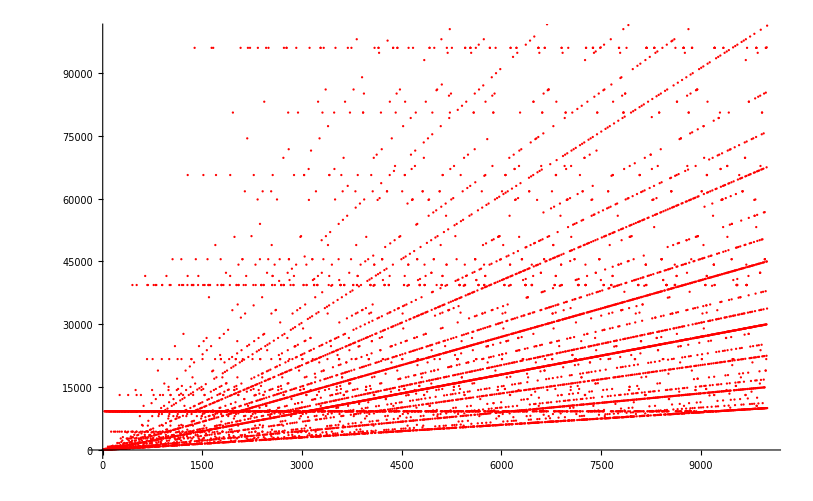

```mathematica
Remove["Global`*"]

Collatz[n_]:=ResourceFunction["Collatz"][n]

maxValues=Table[Max[Collatz[n]],{n,10^4}];

ListPlot[maxValues,PlotStyle->{Red,PointSize[.002]}]
```